```mathematica
(*Found this on StackOverflow*)
(*http://stackoverflow.com/questions/5765491/is-it-possible-to-create-polar-countourplot-listcountourplot-densityplot-in-mathe*)
```

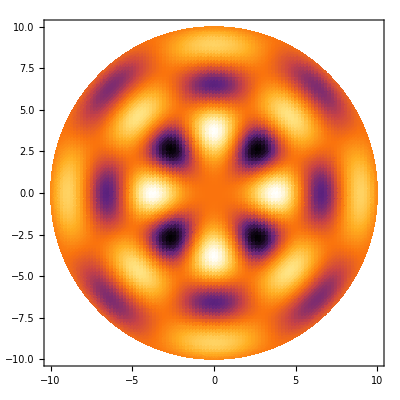

```mathematica
With[{eth=2,er=2,wc=1,m=4},DensityPlot[Re[BesselJ[(Sqrt[eth] m)/Sqrt[er],Sqrt[eth] r wc] Exp[I phi m]]/.{r->Norm[{x,y}],phi->ArcTan[x,y]},{x,-10,10},{y,-10,10},RegionFunction->(#1^2+#2^2<100&),ColorFunction->"SunsetColors",PlotPoints->100]]
```

```mathematica
With[{eth=2,er=2,wc=1,m=4},Plot3D[Re[BesselJ[(Sqrt[eth] m)/Sqrt[er],Sqrt[eth] r wc] Exp[I phi m]]/.{r->Norm[{x,y}],phi->ArcTan[x,y]},{x,-10,10},{y,-10,10},RegionFunction->(#1^2+#2^2<100&),ColorFunction->"SunsetColors",PlotPoints->100]]
```

-Graphics3D-